```mathematica
h[x_]:=Piecewise[{{1+Subscript[c, 0,1] x+Subscript[c, 0,2] x^2+Subscript[c, 0,3] x^3+Subscript[c, 0,4] x^4, 0≤x≤1}, {Subscript[c, 1,1](x-1)+Subscript[c, 1,2](x-1)^2+Subscript[c, 1,3](x-1)^3+Subscript[c, 1,4](x-1)^4, 1<x≤2}, {0, True}}];
f[x_]:=h[Abs[x]];
AllVars={Subscript[c, 0,1],Subscript[c, 0,2],Subscript[c, 0,3],Subscript[c, 0,4],Subscript[c, 1,1],Subscript[c, 1,2],Subscript[c, 1,3],Subscript[c, 1,4]};
```

```mathematica
(*Interpolant constraints*)
I1=f[1]
I2=f[2]
```

1+c_(0,1)+c_(0,2)+c_(0,3)+c_(0,4)

c_(1,1)+c_(1,2)+c_(1,3)+c_(1,4)

```mathematica
(*Partition of unity and linear term*)
T0=CoefficientList[FullSimplify[∑_(k=-1)^2 f[x-k],x>0&&x<1],x]
T1=CoefficientList[FullSimplify[∑_(k=-1)^2 k f[x-k],x>0&&x<1],x]
```

{2+c_(0,1)+c_(0,2)+c_(0,3)+c_(0,4)+c_(1,1)+c_(1,2)+c_(1,3)+c_(1,4),-2 c_(0,2)-3 c_(0,3)-4 c_(0,4)-2 c_(1,2)-3 c_(1,3)-4 c_(1,4),2 c_(0,2)+3 c_(0,3)+6 c_(0,4)+2 c_(1,2)+3 c_(1,3)+6 c_(1,4),-4 c_(0,4)-4 c_(1,4),2 c_(0,4)+2 c_(1,4)}

{1+c_(0,1)+c_(0,2)+c_(0,3)+c_(0,4)+2 c_(1,1)+2 c_(1,2)+2 c_(1,3)+2 c_(1,4),-c_(0,1)-2 c_(0,2)-3 c_(0,3)-4 c_(0,4)-3 c_(1,1)-4 c_(1,2)-6 c_(1,3)-8 c_(1,4),c_(0,2)+3 c_(0,3)+6 c_(0,4)+c_(1,2)+6 c_(1,3)+12 c_(1,4),-c_(0,3)-4 c_(0,4)-3 c_(1,3)-8 c_(1,4),c_(0,4)+c_(1,4)}

```mathematica
GenSols=Solve[{
	I1==0,
	I2==0,
	T0[[1]]==1,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[1]]==0,
	T1[[2]]==1,
	T1[[3]]==0,
	T1[[4]]==0
	},
	AllVars
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c_(0,4)→-1-c_(0,1)-c_(0,2)-c_(0,3),c_(1,1)→-5/3-(5 c_(0,1))/3-(2 c_(0,2))/3-(c_(0,3))/3,c_(1,2)→2+2 c_(0,1)+c_(0,2)+c_(0,3),c_(1,3)→-4/3-(4 c_(0,1))/3-(4 c_(0,2))/3-(5 c_(0,3))/3,c_(1,4)→1+c_(0,1)+c_(0,2)+c_(0,3)}}

```mathematica
RegionXY[k_]:={Quotient[k,2],1+Quotient[-k,2]};
Regions=Table[RegionXY[k],{k,-2,5}]
```

{{-1,2},{-1,1},{0,1},{0,0},{1,0},{1,-1},{2,-1},{2,-2}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
φ=1/2;
W[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF=∑_(i=-3)^5 ∑_(j=-3)^5 W[i-j]f[x-i,y-j]/.GenSol;
SimplifySquare[f_,x0_,y0_]:=Simplify[f,x>x0&&x<x0+1&&y>y0&&y<y0+1];
DSimplifySquare[f_,{x0_,y0_}]:=Simplify[D[SimplifySquare[f,x0,y0],{{x,y}}]];
DSumF=ParallelMap[DSimplifySquare[SumF,#]&,Regions];
```

```mathematica
AnisoInt[df_,{x0_,y0_}]:=Simplify[Integrate[Expand[(df.{1,1})^2],{x,x0,x0+1},{y,y0,y0+1}]];
AnisoInts=Parallelize[MapThread[AnisoInt,{DSumF,Regions}]];
Err=Simplify[Total[AnisoInts]/.φ->1/2]
```

1/6350400(28242002+9203472 c_(0,1)^4+408336 c_(0,2)^4+17110486 c_(0,3)+3681808 c_(0,3)^2+309740 c_(0,3)^3+10461 c_(0,3)^4+8 c_(0,2)^3 (648409+79850 c_(0,3))+4 c_(0,1)^3 (13293824+4151754 c_(0,2)+1567813 c_(0,3))+4 c_(0,2)^2 (6012948+1501989 c_(0,3)+95215 c_(0,3)^2)+2 c_(0,2) (22099269+9321723 c_(0,3)+1175017 c_(0,3)^2+51200 c_(0,3)^3)+4 c_(0,1)^2 (27705822+2836572 c_(0,2)^2+6949914 c_(0,3)+419308 c_(0,3)^2+69 c_(0,2) (264361+31361 c_(0,3)))+2 c_(0,1) (47116758+1743360 c_(0,2)^3+19760445 c_(0,3)+2508664 c_(0,3)^2+104876 c_(0,3)^3+12 c_(0,2)^2 (1399992+168155 c_(0,3))+2 c_(0,2) (25702167+6445542 c_(0,3)+395537 c_(0,3)^2)))

```mathematica
FreeVars=Variables[Err];
DErr=Simplify[D[Err,{FreeVars}]];
H=D[DErr,{FreeVars}];
Sols=Solve[DErr==0,FreeVars,Reals];
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

1 | 0.0493978 | True

```mathematica
RootReduce[Sols[[1]]]
```

$Aborted

{c_(0,4)→-0.0675902,c_(1,1)→-0.38799,c_(1,2)→0.449686,c_(1,3)→-0.129287,c_(1,4)→0.0675902,c_(0,1)→-0.617904,c_(0,2)→-0.432006,c_(0,3)→0.1175}

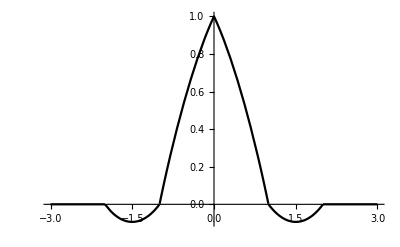

```mathematica
NSol=N[Sols[[1]]];
FullSol=Join[GenSol/.NSol,NSol]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```